```mathematica
Clear["Global`*"]
```

```mathematica
param={eta->0.2,t0->1,vn->2}
```

{eta→0.2,t0→1,vn→2}

```mathematica
AA0=t0 vn^2;
AA2=1+8 eta;
AA4=-9 (eta+4 eta^2);
```

```mathematica
Xp=(p t0 vn^2)/((1-2 eta p^2 vn^2)^(3/2) √(1-(1+2 eta) p^2 vn^2))
```

(p t0 vn^2)/((1-2 eta p^2 vn^2)^(3/2) √(1-(1+2 eta) p^2 vn^2))

```mathematica
Lon=(t0 vn^2 √(1+4 eta p^2 vn^2-6 eta p^4 vn^4-12 eta^2 p^4 vn^4))/((1-2 eta p^2 vn^2)^2 (1-(1+2 eta) p^2 vn^2));
```

```mathematica
Yp=Xp/(vn*t0);
```

```mathematica
pmax=1/(vn*Sqrt[1+2*eta])/.param
```

0.422577

```mathematica
WW1=(t0 vn^2 √(1+4 eta p^2 vn^2-6 eta p^4 vn^4-12 eta^2 p^4 vn^4))/((1-2 eta p^2 vn^2)^2 (1-(1+2 eta) p^2 vn^2));
```

```mathematica
WW2=D[Lon,p]*(1/(D[Yp,p]));
```

```mathematica
CC2=-(WW2-2 AA0 AA2 Y)/(2 AA0 Y-2 WW1 Y+WW2 Y^2)+AA4*(-(2 AA0 Y^2)/(AA0-WW1+AA0 AA2 Y^2))/.Y->Yp/.param;
```

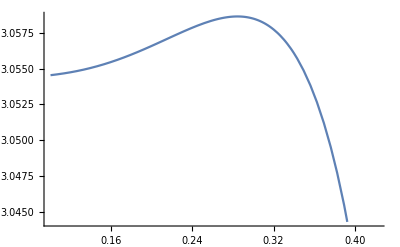

```mathematica
Plot[CC2,{p,0.1,0.4225}]
```

```mathematica
CC4=(WW2-2 AA0 AA2 Y)^2/(Y^2 (2 AA0-2 WW1+WW2 Y)^2)+AA4*((4 AA0)/(AA0-WW1+AA0 AA2 Y^2))/.Y->Yp/.param;
```

```mathematica
C2H=(18 eta (1+4 eta))/(1+8 eta-1/(√(1+2 eta)))+(1+8 eta-1/(√(1+2 eta)))/(1-(1+2 eta)^(3/2) (1+6 eta))/.param
```

3.029

```mathematica
C4H=(-1-8 eta+1/(√(1+2 eta)))^2/((-1+(1+2 eta)^(3/2) (1+6 eta))^2)/.param
```

0.440408

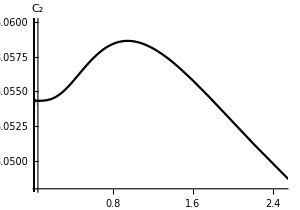
-Graphics-Normalized offset x̂

```mathematica
Labeled[ParametricPlot[{Yp/.param,CC2/.param},{p,0.001,0.442},PlotStyle->{Directive[Black,Thick]},AspectRatio->0.7,PlotRange->{{0.05,2.5},{3.048,3.06}},ImageSize->300,AxesLabel->{Style["",FontSize->18],Style[Text@TraditionalForm@Style[Subscript[C, 2],22,Bold]]},AxesOrigin->{0.05,3.048},AspectRatio->0.7],Text@TraditionalForm@Style[Normalized offset (x̂),20,Bold]]
```

```mathematica
Limit[CC2,p->0]
```

3.05432

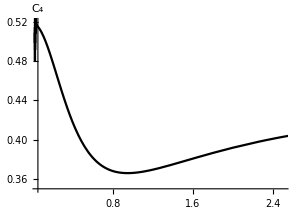
-Graphics-Normalized offset x̂

```mathematica
Labeled[ParametricPlot[{Yp/.param,CC4/.param},{p,0.01,0.442},PlotStyle->{Directive[Black,Thick]},AspectRatio->0.7,PlotRange->{{0.05,2.5},{0.35,0.52}},ImageSize->300,AxesLabel->{Style["",FontSize->18],Style[Text@TraditionalForm@Style[Subscript[C, 4],22,Bold]]},AxesOrigin->{0.05,0.35},AspectRatio->0.7],Text@TraditionalForm@Style[Normalized offset (x̂),20,Bold]]
```

```mathematica
Limit[CC4,p->0]
```

0.517964